```mathematica
Import[NotebookDirectory[]<>"/DensityMatrixTools.wl"]
```

```mathematica
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction = RandomHamiltonian[2,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
```

```mathematica
RandomOrder[]
```

<|𝒬_1→6,𝒬_2→4,𝒬_3→1,𝒬_4→2,𝒬_5→5,𝒬_6→7,𝒬_7→8,𝒬_8→3|>

```mathematica
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>
};
```

<|𝒬_1→5,𝒬_2→6,𝒬_3→3,𝒬_4→4,𝒬_5→1,𝒬_6→2,𝒬_7→7,𝒬_8→8|>

```mathematica
(*ρi = NThermalQBit[Table[Random[],8]];*)
ρi = NThermalQBit[{.2,.2,.2,.2,.5,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
(*RO = RandomOrder[];*)
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,50}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
N[,2]
```

{{22.,22.,22.,22.,0.72,22.,22.,22.},{6.2,6.2,6.2,6.2,0.72,6.2,6.2,6.2},{3.2,3.2,3.2,3.2,0.73,3.2,3.2,3.2},{2.2,2.2,2.2,2.2,0.73,2.2,2.2,2.2},{2.1,2.1,2.1,2.1,0.73,2.1,2.1,2.1},{1.8,1.8,1.8,1.8,0.74,1.8,1.8,1.8},{1.6,1.6,1.6,1.6,0.74,1.6,1.6,1.6},{1.4,1.4,1.4,1.4,0.74,1.4,1.4,1.4},{1.3,1.3,1.3,1.3,0.75,1.3,1.3,1.3},{1.2,1.2,1.2,1.2,0.75,1.2,1.2,1.2},{1.2,1.2,1.2,1.2,0.76,1.2,1.2,1.2},{1.1,1.1,1.1,1.1,0.76,1.1,1.1,1.1},{1.1,1.1,1.1,1.1,0.76,1.1,1.1,1.1},{1.1,1.1,1.1,1.1,0.77,1.,1.1,1.1},{1.,1.,1.,1.,0.77,1.,1.,1.},{1.,1.,1.,1.,0.77,1.,1.,1.},{1.,1.,1.,1.,0.77,0.98,1.,1.},{1.,1.,1.,1.,0.78,0.97,1.,1.},{0.99,0.99,0.99,0.99,0.78,0.96,0.99,0.99},{0.98,0.99,0.98,0.98,0.78,0.96,0.98,0.98},{0.98,0.98,0.97,0.98,0.78,0.95,0.97,0.97},{0.97,0.97,0.97,0.97,0.78,0.94,0.97,0.97},{0.97,0.97,0.96,0.96,0.78,0.94,0.96,0.96},{0.96,0.96,0.95,0.96,0.79,0.93,0.95,0.96},{0.95,0.96,0.95,0.95,0.79,0.93,0.95,0.95},{0.95,0.95,0.95,0.95,0.79,0.92,0.94,0.95},{0.94,0.94,0.94,0.94,0.79,0.92,0.94,0.94},{0.94,0.94,0.94,0.94,0.79,0.91,0.94,0.94},{0.93,0.94,0.93,0.93,0.79,0.91,0.93,0.93},{0.93,0.93,0.93,0.93,0.79,0.91,0.93,0.93},{0.93,0.93,0.93,0.93,0.79,0.9,0.93,0.92},{0.93,0.93,0.93,0.93,0.79,0.9,0.93,0.92},{0.92,0.93,0.93,0.93,0.8,0.9,0.93,0.92},{0.92,0.92,0.93,0.92,0.8,0.9,0.93,0.92},{0.92,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.92,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.92,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.92,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.91,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.91,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.91,0.92,0.92,0.92,0.8,0.9,0.92,0.92},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.92,0.91},{0.91,0.91,0.92,0.91,0.8,0.9,0.91,0.91}}

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

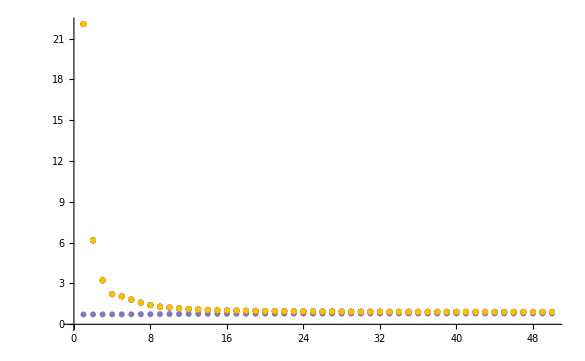

```mathematica
ListPlot[Transpose[Table[Values[temps],{temps,AmbientTemps}]],PlotRange-> All]
```

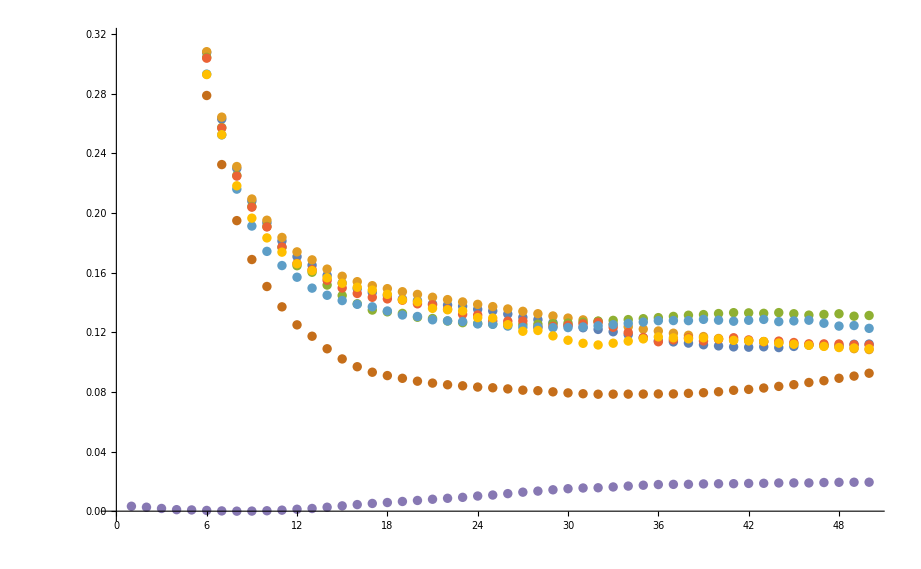

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

```mathematica
(*Table[{r,Total@Unitize@(DMS[[45]][data][[;;,r]]//Normal)},{r,256}]*)
```

```mathematica
(*frames = Show/@Prepend[DMS,ρi];
ListAnimate[frames][[2;;]]
```

```mathematica
(*Export["Gas.gif",frames]
```

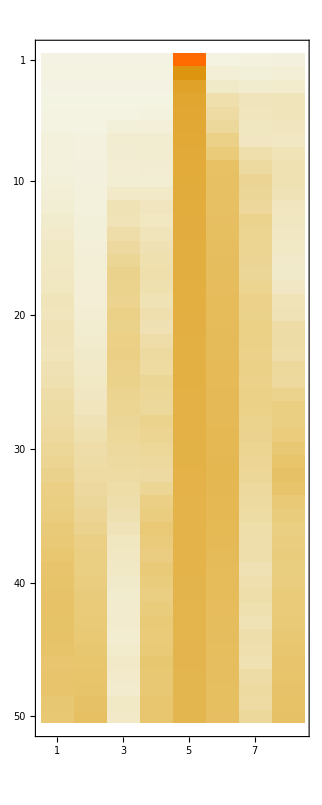

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

```mathematica
Iter1508qbitgas1HighTempInitial;
Iter1508qbitgas1HighTempInitialExtractableWorkOverTime ;
```